### 2.5 Multiedges

Rules can involve several copies of the same relation, corresponding to multiedges in a graph. A simple example is the rule:

```mathematica
{{x,y}}->{{x,z},{x,z},{y,z}}
```

{{x, y}} → {{x, z}, {x, z}, {y, z}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,z},{y,z}}],VertexLabels->Automatic,"RulePartsAspectRatio"-> 0.25]
```

-Graphics-

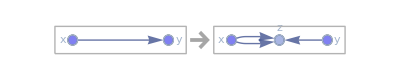

```mathematica
RulePlot[[{{x,y}}->{{x,z},{x,z},{y,z}}], VertexLabels->Automatic]
```

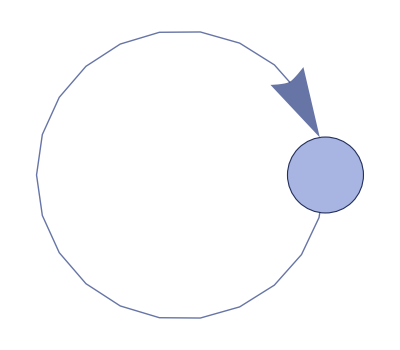
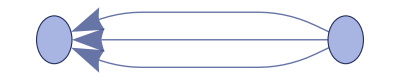
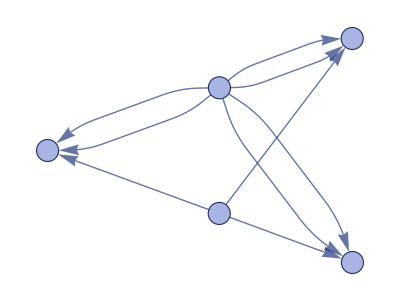
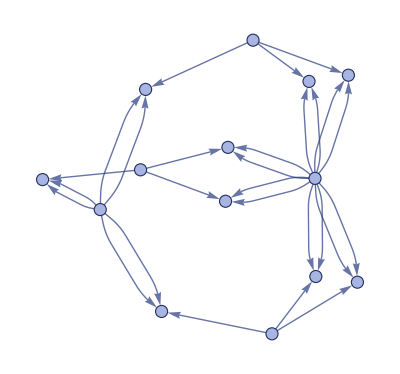

```mathematica
[{{x,y}}->{{x,z},{x,z},{y,z}},{{0,0}},3,"StatesPlotsList"]
```

Running this rule produces a structure with 3^n edges and 1/6(3^(n+1) + 3) nodes at step n:

```mathematica
ResourceFunction["WolframModel"][{{{x,y}}->{{x,z},{x,z},{y,z}}},{{1,1}},5]["StatesPlotsList", "MaxImageSize"->180]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Rules can both create and destroy multiedges. The rule

```mathematica
{{x,y}}->{{x,z},{z,w},{y,z}}
```

{{x, y}} → {{x, z}, {z, w}, {y, z}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{y,z},{z,w}}],VertexLabels->Automatic,"RulePartsAspectRatio"-> 1]
```

-Graphics-

generates a multiedge after one step, but then destroys it:

```mathematica
ResourceFunction["WolframModel"][{{{x,y}}->{{x,z},{z,w},{y,z}}},{{1,1}},5]["StatesPlotsList","MaxImageSize"-> 180]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}